```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=Flatten[Import["./k1.dat"]]/197.33;
lam1=Flatten[Import["./lam1.dat"]];
lam2=Flatten[Import["./lam2.dat"]];
lam1dl=lam1[[1;;Length[k]]]*k^-2;
lam2dl=lam2[[1;;Length[k]]]*k^-1*51.34356;
```

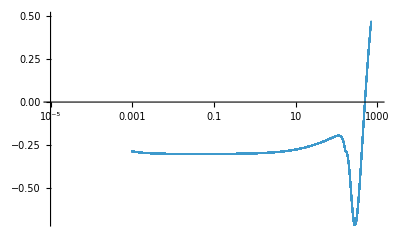

```mathematica
Show[ListPlot[Transpose[{k*197.33,lam1dl}],PlotRange->{{10^-5,1000},{-0.7,0.5}},ScalingFunctions->{"Log",Automatic}]]
```

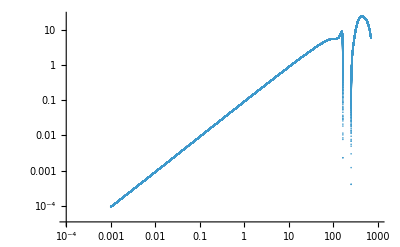

```mathematica
ListPlot[Transpose[{k*197.33,lam2[[1;;Length[k]]]}],PlotRange->{{10^-4,1000},All},ScalingFunctions->{"Log","Log"}]
```